## Two-state mixing

```mathematica
(*The interaction strength between the two states*)
VINT=0.05;
(*The initial separation between the two states*)
DE21=0.1;
RR[de21_,vint_]:=de21/vint;
(*the smaller mixing amplitude β*)
β[r_]:=1/((1+(r/2+Sqrt[1+r^2/4])^2)^(1/2));
```

## Find the inverse of the function β(R)

```mathematica
invbeta[x_]:=InverseFunction[ConditionalExpression[1/((1+(#/2+Sqrt[1+#^2/4])^2)^(1/2)),0.01<#1<12]&][x];
```

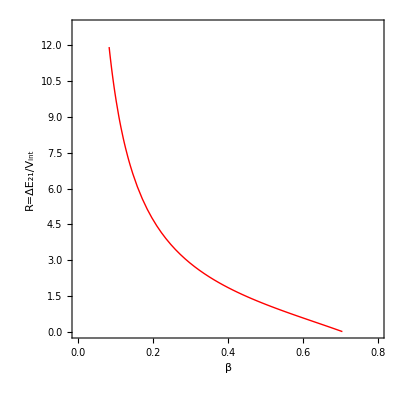

```mathematica
Plot[invbeta[x],{x,0.083,0.705},PlotRange->{{0,0.8},{0,12.8}},AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"β","R=ΔE_21/V_int"},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"}]
```

```mathematica
invbeta[x]
```

ConditionalExpression[√((-1.+4. x^2-4. x^4)/(x^2 (-1.+x^2))), 0.0824805<x<0.705337]